# Bona-fide conditions

```mathematica
ClearAll[g12, gʹ12, g34, gʹ34, wa, wʹa, wb, wʹb]
```

Some initial definitions:

```mathematica
Z=DiagonalMatrix[{1,-1}];
b1[r_]:=Cosh[r]*IdentityMatrix[2];
b2[r_]:=Sinh[r]*Z;
G12=DiagonalMatrix[{g12, gʹ12}];
G34=DiagonalMatrix[{g34, gʹ34}];
```

Eve’s covariance matrix:

```mathematica
VE1E2E3E4=ArrayFlatten[({{wʹa*IdentityMatrix[2], G12, 0, 0}, {G12, wa*IdentityMatrix[2], 0, 0}, {0, 0, wb*IdentityMatrix[2], G34}, {0, 0, G34, wʹb*IdentityMatrix[2]}})]
```

{{wʹa,0,g12,0,0,0,0,0},{0,wʹa,0,gʹ12,0,0,0,0},{g12,0,wa,0,0,0,0,0},{0,gʹ12,0,wa,0,0,0,0},{0,0,0,0,wb,0,g34,0},{0,0,0,0,0,wb,0,gʹ34},{0,0,0,0,g34,0,wʹb,0},{0,0,0,0,0,gʹ34,0,wʹb}}

Compute the bona-fide conditions:

```mathematica
Ω={{0, 1, 0, 0, 0, 0, 0, 0},  {-1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, -1, 0}};
M=I*Ω.VE1E2E3E4;
Abs[Eigenvalues[M]]
```

{(√Abs[-2 gʹ12 g12-wʹa^2-wa^2-√(4 gʹ12 g12 wʹa^2+wʹa^4+4 gʹ12^2 wʹa wa+4 g12^2 wʹa wa+4 gʹ12 g12 wa^2-2 wʹa^2 wa^2+wa^4)])/(√2),(√Abs[-2 gʹ12 g12-wʹa^2-wa^2-√(4 gʹ12 g12 wʹa^2+wʹa^4+4 gʹ12^2 wʹa wa+4 g12^2 wʹa wa+4 gʹ12 g12 wa^2-2 wʹa^2 wa^2+wa^4)])/(√2),(√Abs[-2 gʹ12 g12-wʹa^2-wa^2+√(4 gʹ12 g12 wʹa^2+wʹa^4+4 gʹ12^2 wʹa wa+4 g12^2 wʹa wa+4 gʹ12 g12 wa^2-2 wʹa^2 wa^2+wa^4)])/(√2),(√Abs[-2 gʹ12 g12-wʹa^2-wa^2+√(4 gʹ12 g12 wʹa^2+wʹa^4+4 gʹ12^2 wʹa wa+4 g12^2 wʹa wa+4 gʹ12 g12 wa^2-2 wʹa^2 wa^2+wa^4)])/(√2),(√Abs[-2 gʹ34 g34-wʹb^2-wb^2-√(4 gʹ34 g34 wʹb^2+wʹb^4+4 gʹ34^2 wʹb wb+4 g34^2 wʹb wb+4 gʹ34 g34 wb^2-2 wʹb^2 wb^2+wb^4)])/(√2),(√Abs[-2 gʹ34 g34-wʹb^2-wb^2-√(4 gʹ34 g34 wʹb^2+wʹb^4+4 gʹ34^2 wʹb wb+4 g34^2 wʹb wb+4 gʹ34 g34 wb^2-2 wʹb^2 wb^2+wb^4)])/(√2),(√Abs[-2 gʹ34 g34-wʹb^2-wb^2+√(4 gʹ34 g34 wʹb^2+wʹb^4+4 gʹ34^2 wʹb wb+4 g34^2 wʹb wb+4 gʹ34 g34 wb^2-2 wʹb^2 wb^2+wb^4)])/(√2),(√Abs[-2 gʹ34 g34-wʹb^2-wb^2+√(4 gʹ34 g34 wʹb^2+wʹb^4+4 gʹ34^2 wʹb wb+4 g34^2 wʹb wb+4 gʹ34 g34 wb^2-2 wʹb^2 wb^2+wb^4)])/(√2)}

We see that the symplectic values have analogous expressions for 12 and 34 and that they are completely decoupled. Therefore, we can evaluate separately the bona-fide condition .

We can write the smallest symplectic value (squared) in this compact form:

```mathematica
ν12=0.5 (2 g12 gʹ12+wa^2+wʹa^2-√(4 (g12^2+gʹ12^2) wa wʹa+(wa^2-wʹa^2)^2+4 g12 gʹ12 (wa^2+wʹa^2)));
ν34=0.5 (2 g34 gʹ34+wb^2+wʹb^2-√(4 (g34^2+gʹ34^2) wb wʹb+(wb^2-wʹb^2)^2+4 g34 gʹ34 (wb^2+wʹb^2)));
```

Put some numerical values to do some plots (we do it for the g12 but we would obtain the same results for g34):

```mathematica
wa=1.025;
wʹa=1.025;
feasible12={}
For[i=-200, i<200, i++, g12=i*Sqrt[wa*wʹa]/200;  For[j=-200, j<200, j++, gʹ12=j*Sqrt[wa*wʹa]/200; If[Re[ν12]>=1, AppendTo[feasible12, {g12, gʹ12}]]]]
```

{}

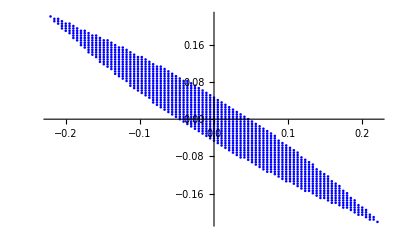

```mathematica
ListPlot[feasible12, AxesLabel->{"", ""}, PlotStyle->Blue]
```

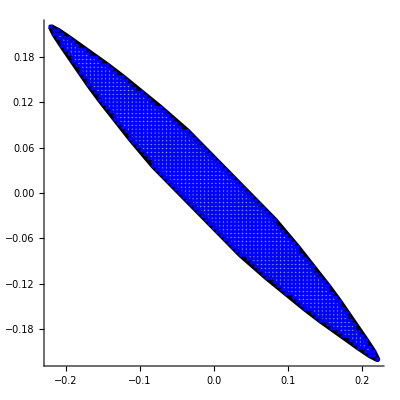

```mathematica
convexHull=ConvexHullMesh[feasible12, MeshCellStyle->{1->{Black, Thickness[0.01]}}];
Show[convexHull,Graphics[{PointSize[0.008],Blue,Point[feasible12]}],Axes->True,AxesLabel->{"", ""}, LabelStyle->{FontSize->16}]
```

```mathematica
Export["goodgraph/bonafide1025.pdf", Show[convexHull,Graphics[{PointSize[0.008],Blue,Point[feasible12]}],Axes->True,AxesLabel->{"", ""}, LabelStyle->{FontSize->16}]];
```